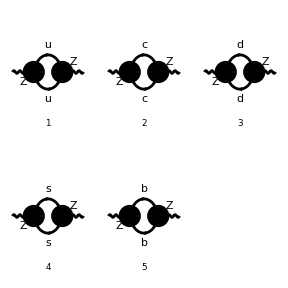

FeynArtsGraphics()(([1] | [2] | [3]
[4] | [5] | Null
Null | Null | Null))

```mathematica
(*creating fermionic loops*)

process1=V[2]-> V[2];
diagzlightquark=InsertFields[topoself,process1,InsertionLevel->{Particles},ExcludeParticles->{F[1],V[1],V[2],V[3],V[4],S[1],S[2],S[3],U[1],U[2],U[3],U[4],SV[2],SV[3],F[2],F[3,{3}]},ExcludeFieldPoints-> FieldPoint[0][V[3],V[3],V[3],V[3]]];
Paint[diagzlightquark,SheetHeader->None,Numbering->Simple]
```

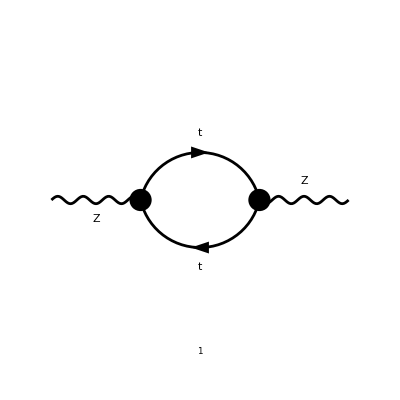

FeynArtsGraphics()(([1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
diagzheavyquark=InsertFields[topoself,process1,InsertionLevel->{Particles},ExcludeParticles->{F[1],V[1],V[2],V[3],V[4],S[1],S[2],S[3],U[1],U[2],U[3],U[4],SV[2],SV[3],F[2],F[3,{1}],F[3,{2}],F[4,{1}],F[4,{2}],F[4,{3}]},ExcludeFieldPoints-> FieldPoint[0][V[3],V[3],V[3],V[3]]];
Paint[diagzheavyquark,SheetHeader->None,Numbering->Simple]
```

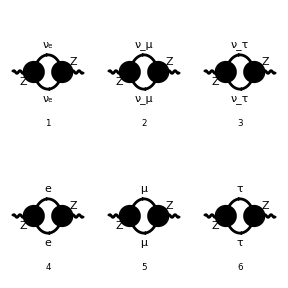

FeynArtsGraphics()(([1] | [2] | [3]
[4] | [5] | [6]
Null | Null | Null))

```mathematica
diagzlepton=InsertFields[topoself,process1,InsertionLevel->{Particles},ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[3],U[1],U[2],U[3],U[4],SV[2],SV[3],F[3],F[4]},ExcludeFieldPoints-> FieldPoint[0][V[3],V[3],V[3],V[3]]];
Paint[diagzlepton,SheetHeader->None,Numbering->Simple]
```

```mathematica
ampzfselflepton=FCFAConvert[CreateFeynAmp[diagzlepton, Truncated-> True, PreFactor ->-1], List-> False, SMP-> True, ChangeDimension->D,
IncomingMomenta->{k},OutgoingMomenta->{k}, LoopMomenta-> {q},DropSumOver-> False, LorentzIndexNames-> {μ,ν},
UndoChiralSplittings-> False, SMP-> True,FinalSubstitutions->{ SMP["m_mu"]-> 0,SMP["m_tau"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0, SMP["e"]->Sqrt[4Pi SMP["alpha_fs"]]}]
```

-(3 tr((-(γ·q)).(ⅈ √π √α γ^ν.(γ̄)^7)/((cos(θ_W)) (sin(θ_W))).(γ·(k-q)).(ⅈ √π √α γ^μ.(γ̄)^7)/((cos(θ_W)) (sin(θ_W)))))/(q^2.(q-k)^2)-(3 tr((-(γ·q)).((2 ⅈ √π √α γ^ν.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))+(2 ⅈ √π √α γ^ν.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(γ·(k-q)).((2 ⅈ √π √α γ^μ.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))+(2 ⅈ √π √α γ^μ.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W))))))/(q^2.(q-k)^2)

```mathematica
ampzfselflightquark=FCFAConvert[CreateFeynAmp[diagzlightquark, Truncated-> True, PreFactor ->-1], List-> False, SMP-> True, ChangeDimension->D,
IncomingMomenta->{k},OutgoingMomenta->{k}, LoopMomenta-> {q},DropSumOver-> False, LorentzIndexNames-> {μ,ν},
UndoChiralSplittings-> False, SMP-> True,FinalSubstitutions->{ SMP["m_mu"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0, SMP["e"]->Sqrt[4Pi SMP["alpha_fs"]]}]
```

-(2 SumOver(Col3,3) tr((-(γ·q)).((2 ⅈ √π √α γ^ν.(γ̄)^7 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))-(4 ⅈ √π √α γ^ν.(γ̄)^6 (sin(θ_W)))/(3 (cos(θ_W)))).(γ·(k-q)).((2 ⅈ √π √α γ^μ.(γ̄)^7 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))-(4 ⅈ √π √α γ^μ.(γ̄)^6 (sin(θ_W)))/(3 (cos(θ_W))))))/(q^2.(q-k)^2)-(3 SumOver(Col3,3) tr((-(γ·q)).((2 ⅈ √π √α γ^ν.(γ̄)^6 (sin(θ_W)))/(3 (cos(θ_W)))+(2 ⅈ √π √α γ^ν.(γ̄)^7 (1/3 (sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(γ·(k-q)).((2 ⅈ √π √α γ^μ.(γ̄)^6 (sin(θ_W)))/(3 (cos(θ_W)))+(2 ⅈ √π √α γ^μ.(γ̄)^7 (1/3 (sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W))))))/(q^2.(q-k)^2)

```mathematica
ampzfselfheavyquark=FCFAConvert[CreateFeynAmp[diagzheavyquark, Truncated-> True, PreFactor ->-1], List-> False, SMP-> True, ChangeDimension->D,
IncomingMomenta->{k},OutgoingMomenta->{k}, LoopMomenta-> {q},DropSumOver-> False, LorentzIndexNames-> {μ,ν},
UndoChiralSplittings-> True, SMP-> True,FinalSubstitutions->{ SMP["m_mu"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0, SMP["e"]->Sqrt[4Pi SMP["alpha_fs"]]}]
```

-(SumOver(Col3,3) tr((m_t-γ·q).((2 ⅈ √π √α γ^ν.(γ̄)^7 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))-(4 ⅈ √π √α γ^ν.(γ̄)^6 (sin(θ_W)))/(3 (cos(θ_W)))).(γ·(k-q)+m_t).((2 ⅈ √π √α γ^μ.(γ̄)^7 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))-(4 ⅈ √π √α γ^μ.(γ̄)^6 (sin(θ_W)))/(3 (cos(θ_W))))))/((q^2-m_t^2).((q-k)^2-m_t^2))

```mathematica
transverselepton=1/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]]). ampzfselflepton//Contract//DiracSimplify;

transverselepton1=-ⅈ/(16 π^2) TID[transverselepton/.DiracTrace-> Tr,q,ToPaVe-> True]//DiracSimplify
```

(3 π α (2-D) k^2 (4 (sin(θ_W))^4-2 (sin(θ_W))^2+1) B_0(k^2,0,0))/(8 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
transverselightquark=1/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]]). ampzfselflightquark//Contract//DiracSimplify;
```

```mathematica
transverselightquark1=-ⅈ/(16 π^2) TID[transverselightquark/.DiracTrace-> Tr,q,ToPaVe-> True,Collecting-> True]/.SumOver[SUNFIndex[Col3],3]-> 3//DiracSimplify
```

(π α (2-D) k^2 (88 (sin(θ_W))^4-84 (sin(θ_W))^2+45) B_0(k^2,0,0))/(48 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
transleptonandlightquark=Collect[transverselepton1+transverselightquark1,B0[Pair[Momentum[k,D],Momentum[k,D]],0,0]]//FullSimplify
```

(π α (D-2) k^2 (40 (4 (sin(θ_W))^2-3) (sin(θ_W))^2+63) B_0(k^2,0,0))/(48 (D-1) (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
transleptonandlightquarkeva=PaXEvaluate[transleptonandlightquark,q]
```

(π α k^2 (160 (sin(θ_W))^4-120 (sin(θ_W))^2+63))/(72 ε (cos(θ_W))^2 (sin(θ_W))^2)+(π α k^2 log(-μ^2/k^2) (160 (sin(θ_W))^4-120 (sin(θ_W))^2+63))/(72 (cos(θ_W))^2 (sin(θ_W))^2)-(π α k^2 (-5+3 ℽ+3 log(π)) (160 (sin(θ_W))^4-120 (sin(θ_W))^2+63))/(216 (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
transleptonandlightquarkeva1=Collect[transleptonandlightquarkeva,(63-120*SMP["sin_W"]^2+160*SMP["sin_W"]^4)]
```

(160 (sin(θ_W))^4-120 (sin(θ_W))^2+63) ((π α k^2)/(72 ε (cos(θ_W))^2 (sin(θ_W))^2)+(π α k^2 log(-μ^2/k^2))/(72 (cos(θ_W))^2 (sin(θ_W))^2)-(π α k^2 (-5+3 ℽ+3 log(π)))/(216 (cos(θ_W))^2 (sin(θ_W))^2))

```mathematica
transverseheavyquark=1/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]]). ampzfselfheavyquark//Contract//DiracSimplify;



rule1={B0[Pair[Momentum[k,D],Momentum[k,D]],SMP["m_t"]^2,SMP["m_t"]^2]-> Δ-Log[SMP["m_t"]^2/μ^2]+Pair[Momentum[k,D],Momentum[k,D]]/(6SMP["m_t"]^2),A0[x_]-> x(Δ-Log[x/μ^2]+1),SMP["e"]^2->4Pi SMP["alpha_fs"],D-> 4};
```

```mathematica
transverseheavyquark1=TID[-ⅈ/(16 π^2) transverseheavyquark/.DiracTrace-> Tr,q,ToPaVe-> True]/.SumOver[SUNFIndex[Col3],3]-> 3
```

1/(48 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)π α B_0(k^2,m_t^2,m_t^2) (-32 D k^2 (sin(θ_W))^4+24 D k^2 (sin(θ_W))^2-9 D k^2+18 D m_t^2+64 k^2 (sin(θ_W))^4-48 k^2 (sin(θ_W))^2+18 k^2-128 m_t^2 (sin(θ_W))^4+96 m_t^2 (sin(θ_W))^2-54 m_t^2)-(π α (2-D) (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9) A_0(m_t^2))/(24 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
totaltransversezz=transleptonandlightquark+transverseheavyquark1
```

1/(48 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)π α B_0(k^2,m_t^2,m_t^2) (-32 D k^2 (sin(θ_W))^4+24 D k^2 (sin(θ_W))^2-9 D k^2+18 D m_t^2+64 k^2 (sin(θ_W))^4-48 k^2 (sin(θ_W))^2+18 k^2-128 m_t^2 (sin(θ_W))^4+96 m_t^2 (sin(θ_W))^2-54 m_t^2)+(π α (D-2) k^2 (40 (4 (sin(θ_W))^2-3) (sin(θ_W))^2+63) B_0(k^2,0,0))/(48 (D-1) (cos(θ_W))^2 (sin(θ_W))^2)-(π α (2-D) (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9) A_0(m_t^2))/(24 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
ΣZZ[k_]=totaltransversezz/.{Pair[Momentum[k,D],Momentum[k,D]]->k^2,SumOver[SUNFIndex[Col3],3]-> 3}
```

1/(48 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)π α B_0(k^2,m_t^2,m_t^2) (-32 D k^2 (sin(θ_W))^4+24 D k^2 (sin(θ_W))^2-9 D k^2+18 D m_t^2+64 k^2 (sin(θ_W))^4-48 k^2 (sin(θ_W))^2+18 k^2-128 m_t^2 (sin(θ_W))^4+96 m_t^2 (sin(θ_W))^2-54 m_t^2)+(π α (D-2) k^2 (40 (4 (sin(θ_W))^2-3) (sin(θ_W))^2+63) B_0(k^2,0,0))/(48 (D-1) (cos(θ_W))^2 (sin(θ_W))^2)-(π α (2-D) (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9) A_0(m_t^2))/(24 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
dΣZZ[k_]=D[totaltransversezz,Pair[Momentum[k,D],Momentum[k,D]]]/.{Pair[Momentum[k,D],Momentum[k,D]]-> k^2}
```

(π α (-32 D (sin(θ_W))^4+24 D (sin(θ_W))^2-9 D+64 (sin(θ_W))^4-48 (sin(θ_W))^2+18) B_0(k^2,m_t^2,m_t^2))/(48 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)+(π α (D-2) (40 (4 (sin(θ_W))^2-3) (sin(θ_W))^2+63) B_0(k^2,0,0))/(48 (D-1) (cos(θ_W))^2 (sin(θ_W))^2)+1/(48 (1-D) (cos(θ_W))^2 (sin(θ_W))^2)π α DB0(k^2,m_t^2,m_t^2) (-32 D k^2 (sin(θ_W))^4+24 D k^2 (sin(θ_W))^2-9 D k^2+18 D m_t^2+64 k^2 (sin(θ_W))^4-48 k^2 (sin(θ_W))^2+18 k^2-128 m_t^2 (sin(θ_W))^4+96 m_t^2 (sin(θ_W))^2-54 m_t^2)+(π α (D-2) k^2 DB0(k^2,0,0) (40 (4 (sin(θ_W))^2-3) (sin(θ_W))^2+63))/(48 (D-1) (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
uvsigzzmz=PaXEvaluateUV[totaltransversezz]/.{SumOver[SUNFIndex[Col3],3]-> 3,Pair[Momentum[k,D],Momentum[k,D]]-> SMP["m_Z"]^2}
```

(π α m_Z^2 (8 (sin(θ_W))^4-6 (sin(θ_W))^2+3))/(3 ε_UV (cos(θ_W))^2 (sin(θ_W))^2)-(3 π α m_t^2)/(8 ε_UV (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
ΣZZ[SMP["m_Z"]]/.{SMP["cos_W"]^2-> 1-SMP["sin_W"]^2}/.SMP["sin_W"]^2-> 1-SMP["m_W"]^2/SMP["m_Z"]^2 /. 1/SMP["cos_W"]^2-> SMP["m_Z"]^2/SMP["m_W"]^2/. 1/SMP["sin_W"]^2-> 1/(1-SMP["m_W"]^2/SMP["m_Z"]^2)/.SMP["sin_W"]^4-> (1-SMP["m_W"]^2/SMP["m_Z"]^2)^2/. 1/(1-SMP["m_W"]^2/SMP["m_Z"]^2)-> SMP["m_Z"]^2/(SMP["m_Z"]^2-SMP["m_W"]^2)//Expand
```

(103 D π B_0(m_Z^2,0,0) α m_Z^6)/(48 (D-1) m_W^2 (m_Z^2-m_W^2))-(103 π B_0(m_Z^2,0,0) α m_Z^6)/(24 (D-1) m_W^2 (m_Z^2-m_W^2))-(17 D π B_0(m_Z^2,m_t^2,m_t^2) α m_Z^6)/(48 (1-D) m_W^2 (m_Z^2-m_W^2))+(17 π B_0(m_Z^2,m_t^2,m_t^2) α m_Z^6)/(24 (1-D) m_W^2 (m_Z^2-m_W^2))-(25 D π B_0(m_Z^2,0,0) α m_Z^4)/(6 (D-1) (m_Z^2-m_W^2))+(25 π B_0(m_Z^2,0,0) α m_Z^4)/(3 (D-1) (m_Z^2-m_W^2))+(5 D π B_0(m_Z^2,m_t^2,m_t^2) α m_Z^4)/(6 (1-D) (m_Z^2-m_W^2))-(5 π B_0(m_Z^2,m_t^2,m_t^2) α m_Z^4)/(3 (1-D) (m_Z^2-m_W^2))+(3 D π B_0(m_Z^2,m_t^2,m_t^2) α m_t^2 m_Z^4)/(8 (1-D) m_W^2 (m_Z^2-m_W^2))-(43 π B_0(m_Z^2,m_t^2,m_t^2) α m_t^2 m_Z^4)/(24 (1-D) m_W^2 (m_Z^2-m_W^2))+(17 D π A_0(m_t^2) α m_Z^4)/(24 (1-D) m_W^2 (m_Z^2-m_W^2))-(17 π A_0(m_t^2) α m_Z^4)/(12 (1-D) m_W^2 (m_Z^2-m_W^2))+(10 π B_0(m_Z^2,m_t^2,m_t^2) α m_t^2 m_Z^2)/(3 (1-D) (m_Z^2-m_W^2))+(10 D π B_0(m_Z^2,0,0) α m_W^2 m_Z^2)/(3 (D-1) (m_Z^2-m_W^2))-(20 π B_0(m_Z^2,0,0) α m_W^2 m_Z^2)/(3 (D-1) (m_Z^2-m_W^2))-(2 D π B_0(m_Z^2,m_t^2,m_t^2) α m_W^2 m_Z^2)/(3 (1-D) (m_Z^2-m_W^2))+(4 π B_0(m_Z^2,m_t^2,m_t^2) α m_W^2 m_Z^2)/(3 (1-D) (m_Z^2-m_W^2))-(5 D π A_0(m_t^2) α m_Z^2)/(3 (1-D) (m_Z^2-m_W^2))+(10 π A_0(m_t^2) α m_Z^2)/(3 (1-D) (m_Z^2-m_W^2))-(8 π B_0(m_Z^2,m_t^2,m_t^2) α m_t^2 m_W^2)/(3 (1-D) (m_Z^2-m_W^2))+(4 D π A_0(m_t^2) α m_W^2)/(3 (1-D) (m_Z^2-m_W^2))-(8 π A_0(m_t^2) α m_W^2)/(3 (1-D) (m_Z^2-m_W^2))

```mathematica
1/π^2 ΣZZ[SMP["m_Z"]]-δMzsq//FullSimplify
```

(α (B_0(m_Z^2,m_t^2,m_t^2) (2 m_t^2 (m_W^4 (16 (sin(θ_W))^2 (4 (cos(θ_W))^2+4 (sin(θ_W))^2-3)-9 (D-3))+m_W^2 m_Z^2 (9 (D-3)-16 (sin(θ_W))^2 (5 (cos(θ_W))^2+4 (sin(θ_W))^2-3))+(43-9 D) m_Z^4 (cos(θ_W))^2 (sin(θ_W))^2)+(D-2) m_Z^2 (m_W^4 (8 (sin(θ_W))^2 (4 (cos(θ_W))^2+4 (sin(θ_W))^2-3)+9)-m_W^2 m_Z^2 (8 (sin(θ_W))^2 (5 (cos(θ_W))^2+4 (sin(θ_W))^2-3)+9)+17 m_Z^4 (cos(θ_W))^2 (sin(θ_W))^2))+(D-2) m_Z^2 B_0(m_Z^2,0,0) (m_W^4 (40 (sin(θ_W))^2 (4 (cos(θ_W))^2+4 (sin(θ_W))^2-3)+63)-m_W^2 m_Z^2 (40 (sin(θ_W))^2 (5 (cos(θ_W))^2+4 (sin(θ_W))^2-3)+63)+103 m_Z^4 (cos(θ_W))^2 (sin(θ_W))^2)-2 (D-2) A_0(m_t^2) (m_W^4 (8 (sin(θ_W))^2 (4 (cos(θ_W))^2+4 (sin(θ_W))^2-3)+9)-m_W^2 m_Z^2 (8 (sin(θ_W))^2 (5 (cos(θ_W))^2+4 (sin(θ_W))^2-3)+9)+17 m_Z^4 (cos(θ_W))^2 (sin(θ_W))^2)))/(48 π (D-1) m_W^2 (cos(θ_W))^2 (m_W^2-m_Z^2) (sin(θ_W))^2)